```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1=Import["massNS.dat","Table"];
```

```mathematica
data2=Import["massWD.dat","Table"];
```

```mathematica
data1//Grid
```

1.559 | 0.005 | 0.005 | 1 | 13 | J0453+1559 | 
1.174 | 0.004 | 0.004 | 1 | 0 | J0453+1559c | 
1.3381 | 0.0007 | 0.0007 | 1 | 6 | J0737-3039A | 
1.2489 | 0.0007 | 0.0007 | 1 | 2 | J0737-3039B | 
1.333 | 0.0004 | 0.0004 | 1 | 5 | B1534+12 | 
1.3455 | 0.0004 | 0.0004 | 1 | 8 | B1534+12c | 
1.341 | 0.007 | 0.007 | 1 | 7 | J1756-2251 | 
1.23 | 0.007 | 0.007 | 1 | 1 | J1756-2251c | 
1.291 | 0.011 | 0.011 | 1 | 3 | J1906+0746 | 
1.322 | 0.011 | 0.011 | 1 | 4 | J1906+0746c | 
1.4398 | 0.0002 | 0.0002 | 1 | 12 | B1913+16 | 
1.3886 | 0.0002 | 0.0002 | 1 | 11 | B1913+16c | 
1.358 | 0.01 | 0.01 | 1 | 10 | B2127+11C | 
1.354 | 0.01 | 0.01 | 1 | 9 | B2127+11Cc | 
1.766 | 0.991 | 0.003 | 1 | 21 | J1518+4904 | 
0.951 | 0.001 | 0.995 | 1 | 14 | J1518+4904c | 
1.478 | 0.71 | 0.137 | 1 | 20 | J1811-1736 | 
1.002 | 0.056 | 0.872 | 1 | 15 | J1811-1736c | 
1.298 | 0.843 | 0.034 | 1 | 18 | J1829+2456 | 
1.273 | 0.019 | 0.872 | 1 | 17 | J1829+2456c | 
1.199 | 0.79 | 0.059 | 1 | 16 | J1930-1852 | 
1.363 | 0.034 | 0.831 | 1 | 19 | J1930-1852c | 
1.4378 | 0.0013 | 0.0013 | 2 | 32 | J0337+1715 | 
2.01 | 0.04 | 0.04 | 2 | 47 | J0348+0432 | 
1.44 | 0.07 | 0.07 | 2 | 33 | J0437-4715 | 
1.53 | 0.2 | 0.1 | 2 | 37 | J0621+1002 | 
1.72 | 0.07 | 0.07 | 2 | 40 | J0751+1807 | 
1.83 | 0.11 | 0.11 | 2 | 42 | J1012+5307 | 
1.928 | 0.007 | 0.007 | 2 | 45 | J1614-2230 | 
1.31 | 0.11 | 0.11 | 2 | 27 | J1713+0747 | 
1.47 | 0.06 | 0.07 | 2 | 36 | J1738+0333 | 
1.24 | 0.11 | 0.11 | 2 | 25 | J1802-2124 | 
1.3655 | 0.0021 | 0.0021 | 2 | 29 | J1807-2500B | 
1.58 | 0.13 | 0.1 | 2 | 38 | B1855+09 | 
1.667 | 0.021 | 0.021 | 2 | 39 | J1903+0327 | 
1.47 | 0.03 | 0.03 | 2 | 35 | J1909-3744 | 
1.3 | 0.2 | 0.2 | 2 | 26 | J1910-5958A | 
1.832 | 0.028 | 0.028 | 2 | 43 | J1946+3417 | 
1.2 | 0.14 | 0.14 | 2 | 23 | J2222-0137 | 
1.393 | 0.013 | 0.013 | 2 | 31 | J2234+0611 | 
1.384 | 0.514 | 0.079 | 2 | 30 | J0024-7204H | 
1.468 | 0.266 | 0.02 | 2 | 34 | J0514-4002A | 
1.965 | 0.498 | 0.243 | 2 | 46 | B1516+02B | 
2.634 | 0.504 | 0.262 | 2 | 48 | J1748-2021B | 
1.877 | 0.535 | 0.042 | 2 | 44 | J1748-2446I | 
1.733 | 0.498 | 0.073 | 2 | 41 | J1748-2446J | 
1.199 | 0.397 | 0.171 | 2 | 22 | J1750-37A | 
1.238 | 0.51 | 0.112 | 2 | 24 | B1802-07 | 
1.343 | 0.547 | 0.019 | 2 | 28 | J1824-2452C | 
1.65 | 0.31 | 0.21 | 3 | 52 | EXO | 1745-248
1.57 | 0.29 | 0.3 | 3 | 50 | 4U | 1608-52
1.77 | 0.28 | 0.25 | 3 | 53 | 4U | 1820-30
1.61 | 0.37 | 0.35 | 3 | 51 | KS | 1731-260
1.81 | 0.37 | 0.25 | 3 | 54 | SAX | J1748.9-2021
1.9 | 0.35 | 0.22 | 3 | 55 | 4U | 1724-207
1.56 | 0.145 | 0.529 | 3 | 49 | Cyg | X-2
2.12 | 0.16 | 0.16 | 4 | 67 | Vela | X-1
1.21 | 0.12 | 0.12 | 4 | 58 | SMC | X-1
1.57 | 0.11 | 0.11 | 4 | 62 | LMC | X-4
1.57 | 0.16 | 0.16 | 4 | 64 | Cen | X-3
1.57 | 0.25 | 0.25 | 4 | 63 | SAX | J1802.7-2017
1.41 | 0.24 | 0.24 | 4 | 61 | XTE | J1855-026
1.91 | 0.45 | 0.45 | 4 | 66 | EXO | 1722-363
1.74 | 0.3 | 0.3 | 4 | 65 | OAO | 1657-415
1.073 | 0.358 | 0.358 | 4 | 57 | Her | X-1
1.02 | 0.17 | 0.17 | 4 | 56 | 4U1538-52 | 
1.367 | 0.093 | 0.058 | 4 | 60 | B2303+46 | 
1.27 | 0.01 | 0.01 | 4 | 59 | J1141-6545 |

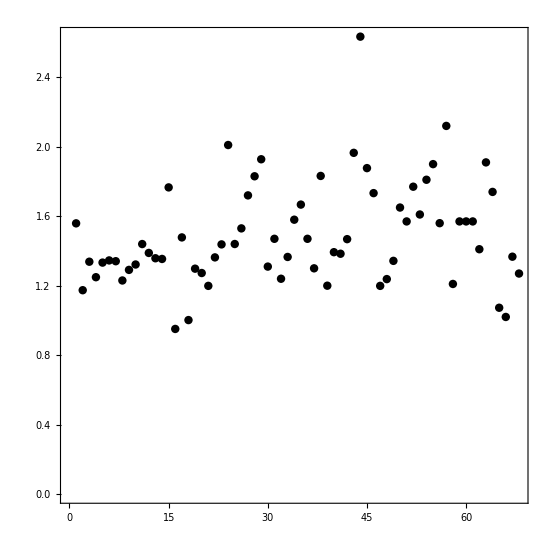

```mathematica
p=ListPlot[Table[{i,data1[[i,1]]},{i,1,Length[data1]}],Frame->True,Joined->False,ImageSize->550,PlotStyle->Darker[Black],FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],AspectRatio->1,FillingStyle->Darker[Red]]
```

```mathematica
myticks2={{{{0,"0"},{1,""},{2,""},{3,""},{4,""},{5,"5",{0.015,0}},{6,""},{7,""},{8,""},{9,""},{10,"10",{0.015,0}},{11,""},{12,""},{13,""},{14,""},{15,"15",{0.015,0}},{16,""}}, {{0,""},{1,""},{2,""},{3,""},{4,""},{5,"",{0.015,0}},{6,""},{7,""},{8,""},{9,""},{10,"",{0.015,0}},{11,""},{12,""},{13,""},{14,""},{15,"",{0.015,0}},{16,""}}},{Automatic,Automatic}};
```

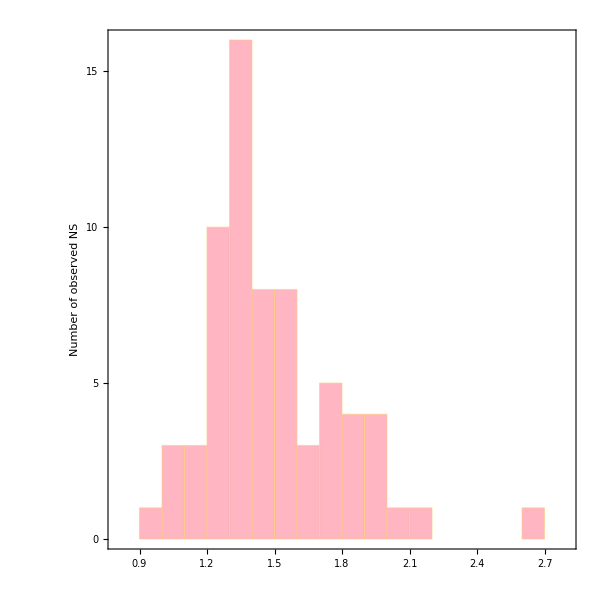

```mathematica
p1=Histogram[data1[[All,1]],15,Frame->True,ImageSize->600,FrameStyle->Directive[18, "Times",Black,Thickness[0.003]],AspectRatio->1.0,ChartStyle->{RGBColor["#FFB5C2"]},PlotRange->{{0.8,2.8},Automatic},FrameTicksStyle->24,FrameTicks->myticks2,FrameLabel->{Style["",FontSize->28],Style["Number of observed NS",FontSize->28]},ImagePadding->{{Automatic,20},{100,20}}]
```

```mathematica
myticks={{{{10,"10"},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"10^2",{0.015,0}},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"10^3",{0.015,0}},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10^4,"10^4",{0.015,0}},{20000,""}}, {{10,""},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"",{0.015,0}},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"",{0.015,0}},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10^4,"",{0.015,0}},{20000,""}}},{Automatic,Automatic}};
```

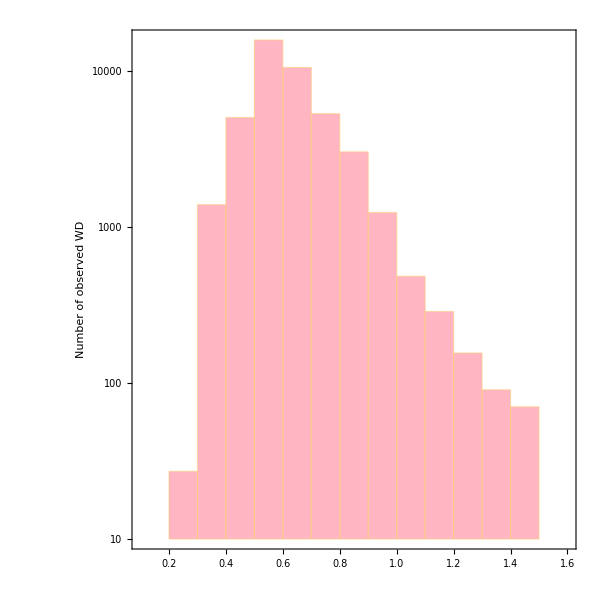

```mathematica
p2=Histogram[data2[[All,1]],15,Frame->True,ImageSize->600,FrameStyle->Directive[18, "Times",Black,Thickness[0.003]],AspectRatio->1,ScalingFunctions->"Log",ChartStyle->{RGBColor["#FFB5C2"]},PlotRange->{{0.1,1.6},Automatic},FrameTicksStyle->24,FrameTicks->myticks,FrameLabel->{Style["",FontSize->28],Style["Number of observed WD",FontSize->28]},ImagePadding->{{Automatic,20},{100,20}}]//Quiet

(*Do not run it in Mathematica 12.0*)
```

```mathematica
q1=Show[p1,Graphics[Rotate[Text[Style["Mass [M_⊙]",FontSize->28],Scaled[{0.5,-0.11}]],0 Degree]]]
```

-Graphics-

```mathematica
q2=Show[-Graphics-,Graphics[Rotate[Text[Style["Mass [M_⊙]",FontSize->28],Scaled[{0.5,-0.11}]],0 Degree]]]
```

-Graphics-

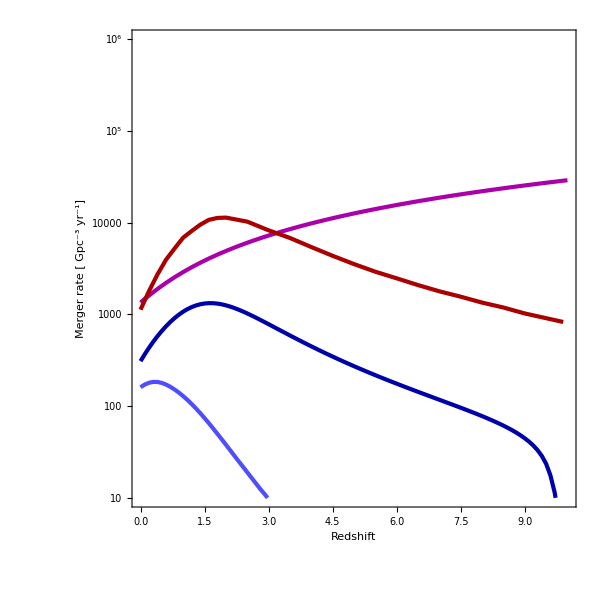
```mathematica
GraphicsRow[{-Graphics-,-Graphics-,-Graphics-},ImageSize->2000,AspectRatio->0.3]
```

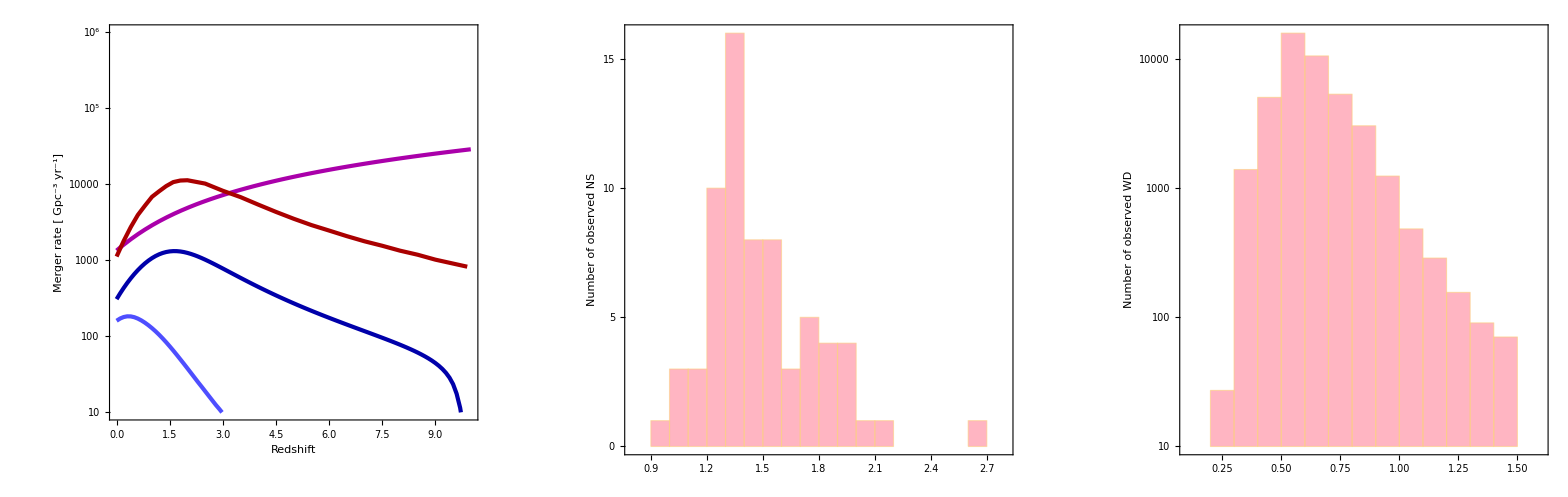

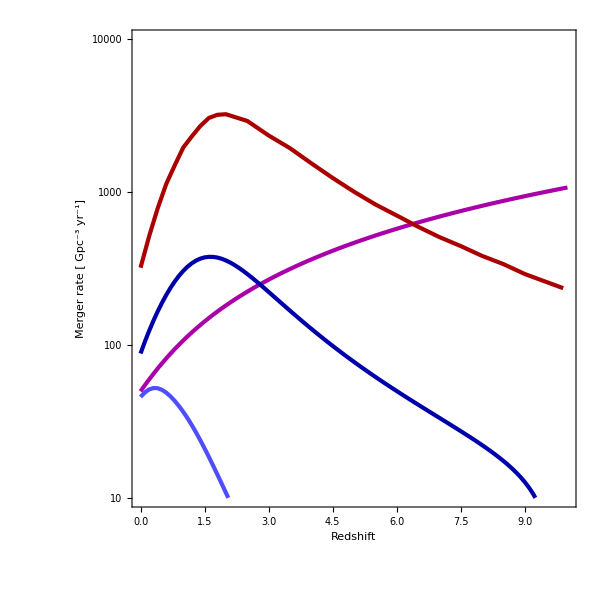
```mathematica
GraphicsRow[{-Graphics-,-Graphics-,-Graphics-},ImageSize->2000,AspectRatio->0.3]
```